# Метод на Нютон (допирателните)

f(x) = 0, x^* = ?

x_0, x_1,x_2 ..... x_n1

Стъпки за решаване:

1. Локализация
2. Проверка на условията за сходимост (f’(x) и f’’(x) да са с постоянен знак в избрания интервал [a, b])
3. X_(n + 1) = X_n - (f(x_n))/(f'(x_n)), n = 0,1,2 ....... (Итерационен процес)
4. Оценка на грешката
E_n = |x^* - x_n| <= M_2/(2 m_1) * |x_n - x_(n-1)| - квадратична сходимост

Задача:
(x^2+ 8)/(x - 2) = 38sinx + 4x
(x^2+ 8)/(x - 2) - 38sinx - 4x = 0
Допустима област (ДО): x - 2 != 0 => x != 2

```mathematica
f[x_] := (x^2+ 8)/(x - 2)-38Sin[x]-4x
```

```mathematica
f[x]
```

-4 x+(8+x^2)/(-2+x)-38 Sin[x]

# 1. Локализация

```mathematica
a = -20;
b = 20;
```

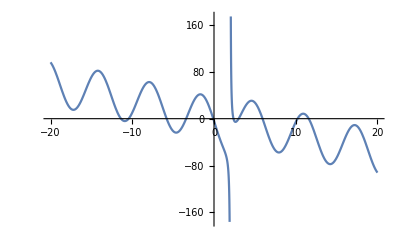

```mathematica
Plot[f[x], {x, a, b}]
```

Брой корени: 10

# 2. Търсим най-големия корен

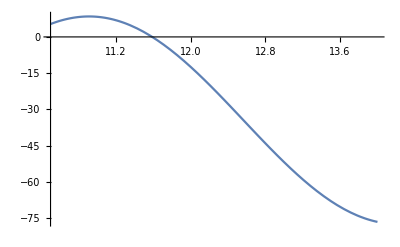

```mathematica
Plot[f[x], {x,10.5, 14}]
```

```mathematica
f[10.5]
```

5.3402

```mathematica
f[14.]
```

-76.6431

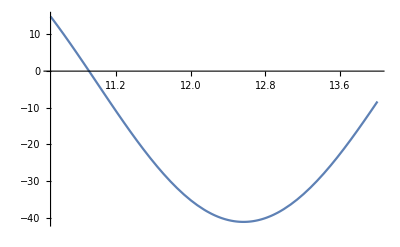

```mathematica
Plot[f'[x], {x,10.5, 14}]
```

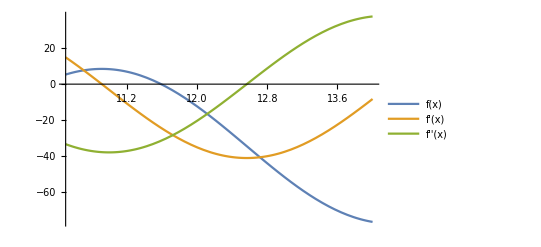

```mathematica
Plot[{f[x],f'[x], f''[x]}, {x,10.5, 14}, PlotLegends->"Expressions"]
```

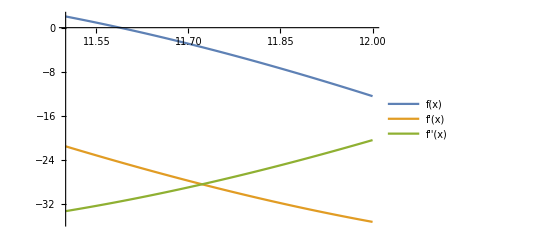

```mathematica
Plot[{f[x],f'[x], f''[x]}, {x,11.5, 12}, PlotLegends->"Expressions"]
```

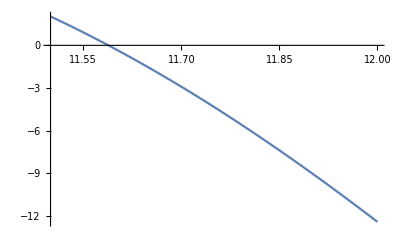

```mathematica
Plot[f[x], {x, 11.5 , 12}]
```

```mathematica
f[11.5]
```

2.03034

```mathematica
f[12.0]
```

-12.4102

Извод:
1. f(11.5) = 2.03.. > 0
2. f(12.0) = -12.41.... < 0
Следователно в двата края на функцията има различни знаци и функцията е непрекъсната в избрания интервал [11,5;12] (точка x = 2 Э [11,5, 12]). Следва, че функцията има поне един корен в дадения интервал.

# 3. Проверка на условията за сходимост

### Проверка на първата производна

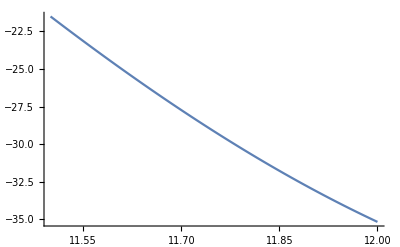

```mathematica
Plot[f'[x], {x, 11.5 , 12}]
```

(1). Следва, че f’(x) има постоянен знак в дадения интервал.

### Проверка на втората производна

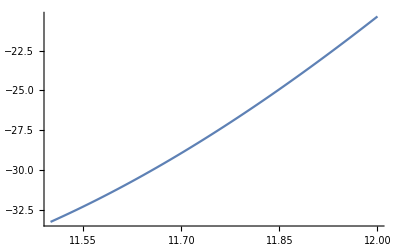

```mathematica
Plot[f''[x], {x, 11.5 , 12}]
```

(2). Следва, че f’’(x) има постоянен знак в дадения интервал.

Извод: от (1) и (2) следва, че f’(x) и f’’(x) са с постоянни знаци в разглеждания интервал [11,5; 12] => Методът на допирателните е сходящ.

# 4. Избор на начално приближение

f(x_0) * f’’ > 0
=> f(x_0) < 0
=> x_0 = 12

### Пресмятане на постоянните величини:

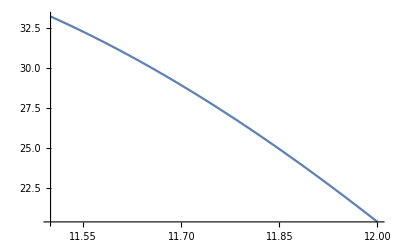

```mathematica
Plot[Abs[f''[x]], {x, 11.5 , 12}]
```

От геометрични съображения максимума се достига в левия край на интервала, а минимума - в десния.

```mathematica
М2 = Abs[f''[11.5]]
```

33.2392

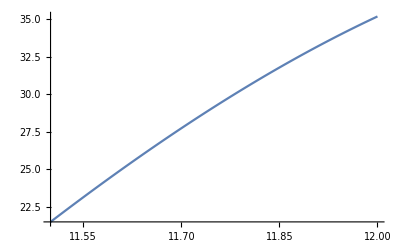

```mathematica
Plot[Abs[f'[x]], {x, 11.5 , 12}]
```

От геометрични съображения максимума се достига в десния край на интервала, а минимума - в левия.

```mathematica
m1 = Abs[f'[11.5]]
```

21.4985

```mathematica
p = М2/(2m1)
```

0.773057

```mathematica
f'[12.0]
```

-35.1865

```mathematica
12 - -12.4102/-35.1865
```

11.6473

```mathematica
f[11.647302232390263]
```

-1.48663

```mathematica
f'[11.647302232390263]
```

-26.1783

```mathematica
p*Abs[12 - 11.647302232390263]
```

0.272655

# 5. Итерации